# Plot SRLDP from cold plasma theory

```mathematica
coldCoefs[x_]:=Module[{ne,b,x0},x0=x;
ne=nprof[x0];
b=bprof[x0];
		SRLDP[freq,ne,b,nz,etaList]]
```

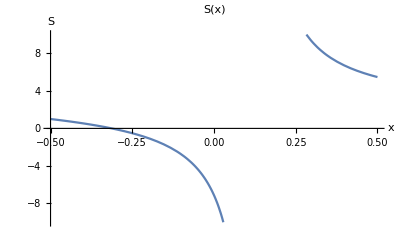

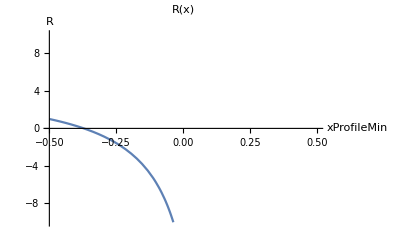

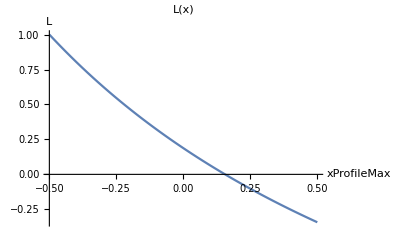

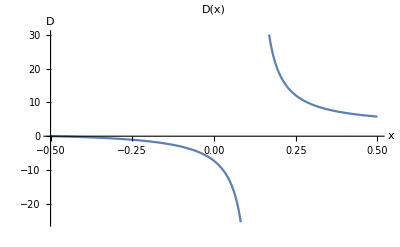

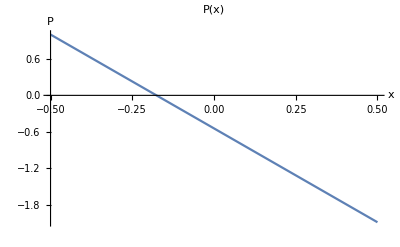

dataSet=NSTX slab

xProfileMin=-0.5

xProfileMax=0.5

nXmin=0.

nXmax=3.×10^19

BXmin=0.5

BXmax=1.3

freq=28000

nz=0.2

etaList={0.,1.,0.,0.,0.}

xmin=-0.5

xmin=-0.5

```mathematica
sPlot=Plot[coldCoefs[x]⟦1⟧,{x,xmin,xmax},AxesOrigin->{xmin,0.}, PlotLabel->"S(x)", AxesLabel->{"x","S"},PlotRange->{-10.,10.}]
rPlot=Plot[coldCoefs[x]⟦2⟧,{x,xmin,xmax},AxesOrigin->{xmin,0.}, PlotLabel->"R(x)", AxesLabel->{"xProfileMin","R"},PlotRange->{-10.,10.}]
lPlot=Plot[coldCoefs[x][[3]],{x,xmin,xmax},AxesOrigin->{xmin,0.}, PlotLabel->"L(x)", AxesLabel->{"xProfileMax","L"}]
dPlot=Plot[coldCoefs[x]⟦4⟧,{x,xmin,xmax},AxesOrigin->{xmin,0.}, PlotLabel->"D(x)", AxesLabel->{"x","D"}]
pPlot=Plot[coldCoefs[x]⟦5⟧,{x,xmin,xmax},AxesOrigin->{xmin,0.}, PlotLabel->"P(x)", AxesLabel->{"x","P"}]
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,xmin,xmin}];
```

## Plot SRLP minus nz^2

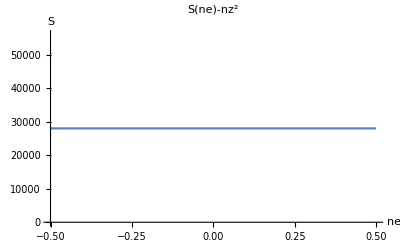

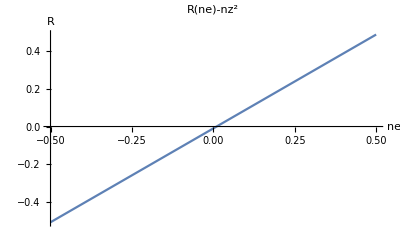

-Graphics-

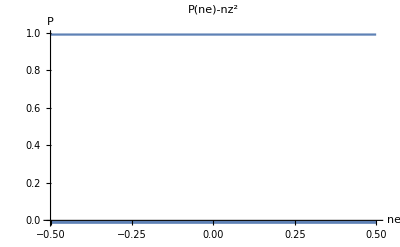

```mathematica
sPlot2=Plot[srldp[freq,x,B0]⟦1⟧-nz^2,{x,xmin,xmax},AxesOrigin->{xmin,0.}, PlotLabel->"S(ne)-nz^2", AxesLabel->{"ne","S"}]
rPlot2=Plot[srldp[freq,x,B0]⟦2⟧-nz^2,{x,xmin,xmax},AxesOrigin->{xmin,0.}, PlotLabel->"R(ne)-nz^2", AxesLabel->{"ne","R"}]
lPlot2=Plot[srldp[freq,x,B0]⟦3⟧-nz^2,{x,xmin,xmax},AxesOrigin->{xmin,0.}, PlotLabel->"L(ne)-nz^2", AxesLabel->{"ne","L"}]
pPlot2=Plot[srldp[freq,x,B0]⟦4⟧-nz^2,{x,xmin,xmax},AxesOrigin->{xmin,0.}, PlotLabel->"P(ne)-nz^2", AxesLabel->{"ne","P"}]
```